# Global Sensitivity Analysis (GSA) INSERT REF NUMBER

Version: 1.0
Author: P. Monks
Date: 18/04/16

This notebook is designed to carry out an uncertainty quantification (UQ) and global sensitivity analysis (GSA) on a set of data provided by the user. It uses the technique described by Hynes in AWE Report XXX, equation XXX.

The data must be provided in a multi-sheet spreadsheet, with each sheet corresponding to a variable (which may be input or output). The user may provide multiple output variables (e.g. f1, f2, f3...), and each of these must have its own sheet at the front of the spreadsheet. If multiple settings are provided for each output (e.g. f1 at t=1, t=2, t=3... and the same for f2), then the settings must be provided in different columns in the appropriate worksheet. The data must not contain different numbers of settings for each output variable - in that case, separate analyses should be carried out for each output variable.

The spreadsheet “ExampleData.xls” provides an example of how to format the spreadsheet. There are two output variables (f1 and f2), and each has data at three settings (t=1, 2 and 3). There are 7 input parameters (x,y,z,a,b,c,d), and these are provided after the output variables.

## Uncertainty Quantification

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["HypothesisTesting`"];
```

#### Options - change the details here; nowhere else

The user must provide some information regarding the data.

```mathematica
DataFile="ExampleData.xls"; (* Provide the name of the input data file. Each variable should be given its own worksheet. Multiple settings of an output variable (e.g. outputs at different times) should be provided on the same worksheet but in separate columns. IMPORTANT: there must be no headers in the columns - data only! *)
Labels={"f1","f2","x","y","z","a","b","c","d"}; (* Provide the labels for the variables. Note the format for multi-column worksheets *)
SettingsVals=Table[t,{t,3}]; (* Provide the settings values (e.g. time values). If there is only one value, provide it with curly brackets, e.g. "{1}" *)
SettingsUnits="Time / hours"; (* Provide the settings units label *)
Outputs=2; (* Specify how many worksheets correspond to output data. IMPORTANT: outputs should be provided before inputs in the spreadsheet *)
```

#### Import and Analyse Data

```mathematica
data=Import[DataFile,"XLS"];
Nouts=Outputs;
Nins=Length[data]-Nouts;
Nsets=Length[data[[1,1]]];
Nruns=Length[data[[1]]];
outs={};Do[AppendTo[outs,Table[data[[outvar,;;,setting]],{setting,Nsets}]],{outvar,Nouts}];
outlabels=Table[Table[Labels[[outvar]]<>"_"<>ToString[setting],{setting,Nsets}],{outvar,Nouts}];
ins={};Do[AppendTo[ins,Flatten[Table[data[[invar+Nouts,i]],{i,Nruns}]]],{invar,Nins}];
inlabels=Labels[[Nouts+1;;Nouts+Nins]];
```

Do some simple summary statistics on the data

```mathematica
Min[outs[[1,1]]]
```

-315125.

```mathematica
UQoutheaders={SettingsUnits,"Minimum","Maximum","Mean","Median","St. Dev.","St. Err.","95 % CI (Lower)","95 % CI (Upper)","5th Quart.","95th Quart."};
```

```mathematica
UQinheaders={"Input","Minimum","Maximum","Mean","Median","St. Dev.","St. Err.","95 % CI (Lower)","95 % CI (Upper)","5th Quart.","95th Quart."};
```

```mathematica
Do[UQouts[outvar]=Prepend[Table[{setting,Min[outs[[outvar,setting]]],Max[outs[[outvar,setting]]],Mean[outs[[outvar,setting]]],Median[outs[[outvar,setting]]],StandardDeviation[outs[[outvar,setting]]],StandardDeviation[outs[[outvar,setting]]]/Sqrt[Nruns],MeanCI[outs[[outvar,setting]]][[1]],MeanCI[outs[[outvar,setting]]][[2]],Quantile[outs[[outvar,setting]],0.05],Quantile[outs[[outvar,setting]],0.95]},{setting,Nsets}],Table[Style[UQoutheaders[[i]],14,Bold,FontFamily->"Helvetica"],{i,Length[UQoutheaders]}]],{outvar,Nouts}];
```

```mathematica
UQins=Prepend[Table[{inlabels[[invar]],Min[ins[[invar]]],Max[ins[[invar]]],Mean[ins[[invar]]],Median[ins[[invar]]],StandardDeviation[ins[[invar]]],StandardDeviation[ins[[invar]]]/Sqrt[Nruns],MeanCI[ins[[invar]]][[1]],MeanCI[ins[[invar]]][[2]],Quantile[ins[[invar]],0.05],Quantile[ins[[invar]],0.95]},{invar,Nins}],Table[Style[UQinheaders[[i]],14,Bold,FontFamily->"Helvetica"],{i,Length[UQinheaders]}]];
```

```mathematica
UQouttabs:=Module[{},Do[Print[Style["UQ - Output: "<>Labels[[outvar]],16,Bold,FontFamily->"Helvetica"]];
Print[UQouts[outvar]//TableForm],{outvar,Nouts}]];
```

```mathematica
UQintabs:=Module[{},Print[Style["UQ - Inputs",16,Bold,FontFamily->"Helvetica"]];
Print[UQins//TableForm]];
```

```mathematica
Export["UQ.xls",{"Inputs"->ReplacePart[UQins,1->UQinheaders],"Outputs"->Flatten[Join[Table[ReplacePart[UQouts[outvar],1->UQoutheaders],{outvar,Nouts}]],1]},"XLS"]
```

UQ.xls

Histograms of outputs (settings extend horizontally, variables extend vertically):

```mathematica
outhists=Table[Table[Histogram[outs[[outvar,setting]],PlotRange->All,ChartStyle->Directive[{Red,Opacity[0.4]}],Frame->True,FrameStyle->Directive[{12,FontFamily->"Helvetica"}],FrameLabel->{Style[If[Nsets==1,Labels[[outvar]],outlabels[[outvar,setting]]],16,Bold,FontFamily->"Helvetica"],Style["Frequency",16,Bold,FontFamily->"Helvetica"]},ImageSize->500],{setting,Nsets}],{outvar,Nouts}]//TableForm;
Export["OutputsHistograms.png",outhists];
```

Histograms of inputs (variables extend horizontally):

```mathematica
inhists={Table[Histogram[ins[[invar]],PlotRange->All,ChartStyle->Directive[{Blue,Opacity[0.4]}],Frame->True,FrameStyle->Directive[{12,FontFamily->"Helvetica"}],FrameLabel->{Style[inlabels[[invar]],16,Bold,FontFamily->"Helvetica"],Style["Frequency",16,Bold,FontFamily->"Helvetica"]},ImageSize->500],{invar,Nins}]}//TableForm;
Export["InputsHistograms.png",inhists];
```

Scatterplots (each output variable has its own set of plots within a frame (extending vertically), settings extend horizontally within a frame, input variables extend vertically within a frame):

```mathematica
scatter={};
Do[AppendTo[scatter,Grid[Table[Table[ListPlot[Table[{ins[[invar,i]],outs[[outvar,setting,i]]},{i,Nruns}],PlotRange->All,PlotStyle->Black,Frame->True,Axes->False,FrameStyle->Directive[{12,FontFamily->"Helvetica"}],FrameLabel->{Style[inlabels[[invar]],16,Bold,FontFamily->"Helvetica"],Style[If[Nsets==1,Labels[[outvar]],outlabels[[outvar,setting]]],16,Bold,FontFamily->"Helvetica"]},AspectRatio->1,ImageSize->400],{setting,Nsets}],{invar,Nins}],Frame->True]
],{outvar,Nouts}];
Do[Export["ScatterPlots_"<>Labels[[outvar]]<>".png",scatter[[outvar]]],{outvar,Nouts}];
```

#### Display UQ Results

```mathematica
UQintabs
UQouttabs
```

UQ - Inputs

Input | Minimum | Maximum | Mean | Median | St. Dev. | St. Err. | 95 % CI (Lower) | 95 % CI (Upper) | 5th Quart. | 95th Quart.
x | 94.2372 | 106.664 | 100.391 | 100.291 | 3.67059 | 0.116074 | 100.163 | 100.619 | 94.846 | 106.146
y | 66.0522 | 134.17 | 100.265 | 100.539 | 20.1813 | 0.638189 | 99.0128 | 101.517 | 69.3494 | 131.267
z | 2061. | 2083.96 | 2072.58 | 2073. | 6.77684 | 0.214303 | 2072.16 | 2073. | 2062.05 | 2082.82
a | -3741.94 | 27725.1 | 11678.3 | 11799.5 | 9228.79 | 291.84 | 11105.6 | 12251. | -2691.79 | 26165.1
b | 681.235 | 1298.02 | 982.114 | 978.621 | 179.75 | 5.68418 | 970.96 | 993.268 | 706.571 | 1262.95
c | 164.025 | 197.965 | 181.286 | 181.144 | 9.72543 | 0.307545 | 180.682 | 181.889 | 165.686 | 196.627
d | 164.009 | 197.952 | 180.904 | 181.253 | 9.81318 | 0.31032 | 180.295 | 181.513 | 165.551 | 196.117

UQ - Output: f1

Time / hours | Minimum | Maximum | Mean | Median | St. Dev. | St. Err. | 95 % CI (Lower) | 95 % CI (Upper) | 5th Quart. | 95th Quart.
1 | -315125. | 3.06415×10^6 | 1.27011×10^6 | 1.27664×10^6 | 928578. | 29364.2 | 1.21249×10^6 | 1.32773×10^6 | -175657. | 2.7252×10^6
2 | 36117.9 | 3.44279×10^6 | 1.64584×10^6 | 1.65455×10^6 | 928382. | 29358. | 1.58823×10^6 | 1.70345×10^6 | 206973. | 3.10181×10^6
3 | 387361. | 3.82144×10^6 | 2.02157×10^6 | 2.03818×10^6 | 928627. | 29365.8 | 1.96395×10^6 | 2.0792×10^6 | 582725. | 3.48427×10^6

UQ - Output: f2

Time / hours | Minimum | Maximum | Mean | Median | St. Dev. | St. Err. | 95 % CI (Lower) | 95 % CI (Upper) | 5th Quart. | 95th Quart.
1 | 756140. | 3.53366×10^6 | 1.91092×10^6 | 1.85038×10^6 | 743649. | 23516.2 | 1.86477×10^6 | 1.95707×10^6 | 884396. | 3.14311×10^6
2 | 774656. | 3.55289×10^6 | 1.92912×10^6 | 1.86764×10^6 | 743597. | 23514.6 | 1.88298×10^6 | 1.97526×10^6 | 905173. | 3.15995×10^6
3 | 793173. | 3.57213×10^6 | 1.94732×10^6 | 1.8849×10^6 | 743547. | 23513. | 1.90118×10^6 | 1.99346×10^6 | 923595. | 3.1768×10^6

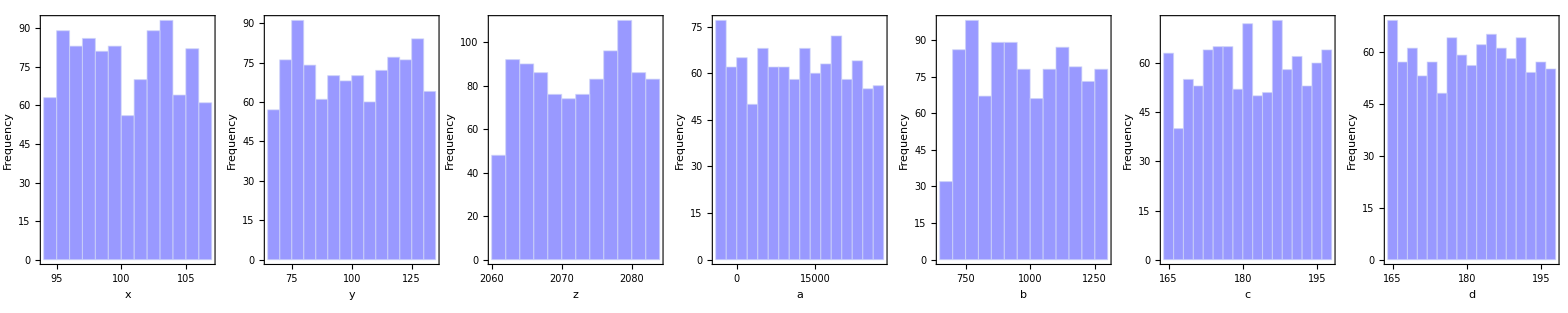

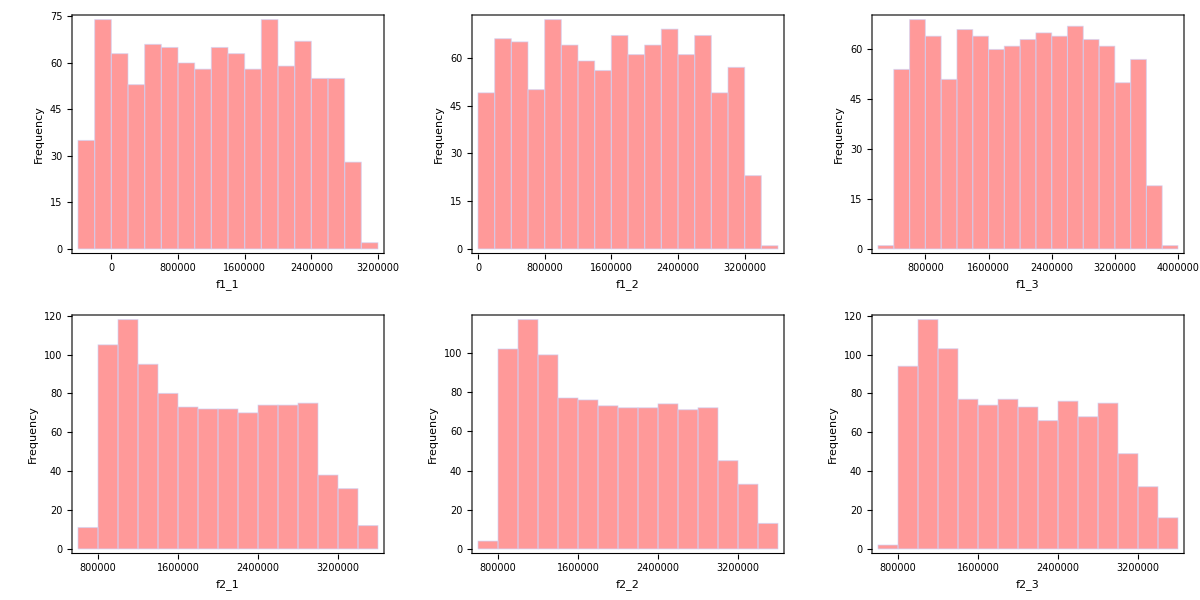

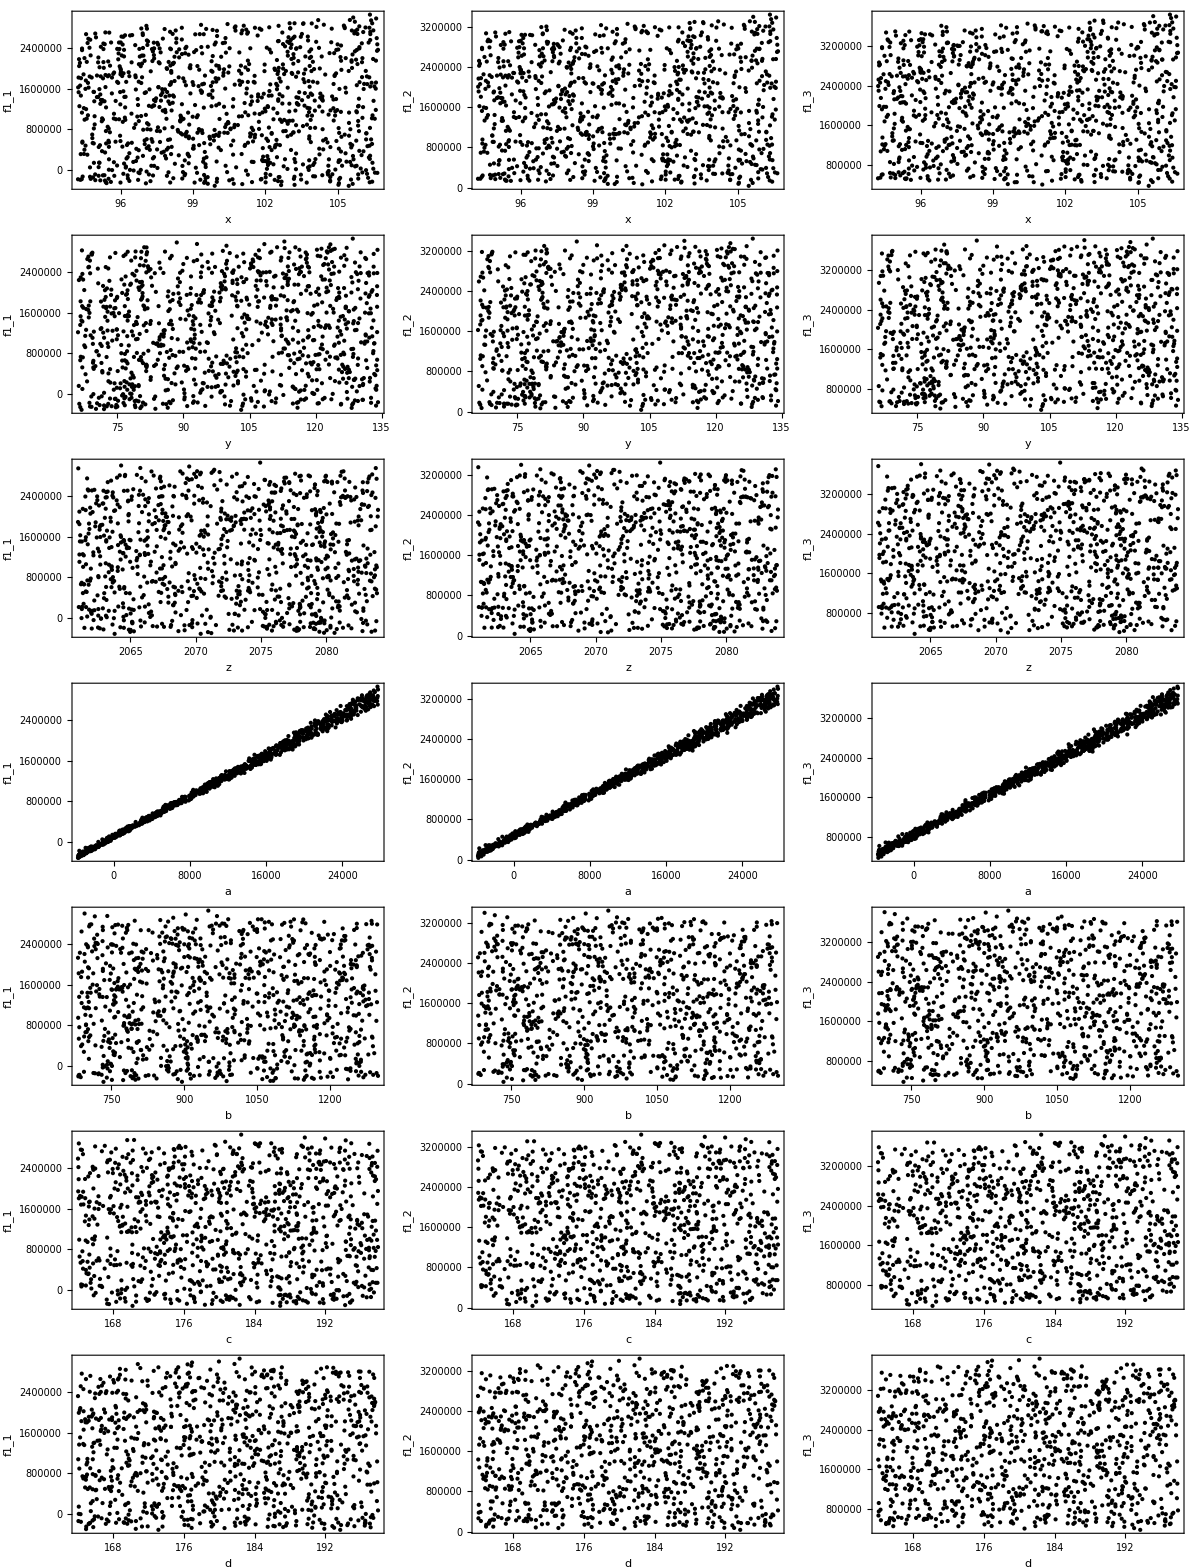
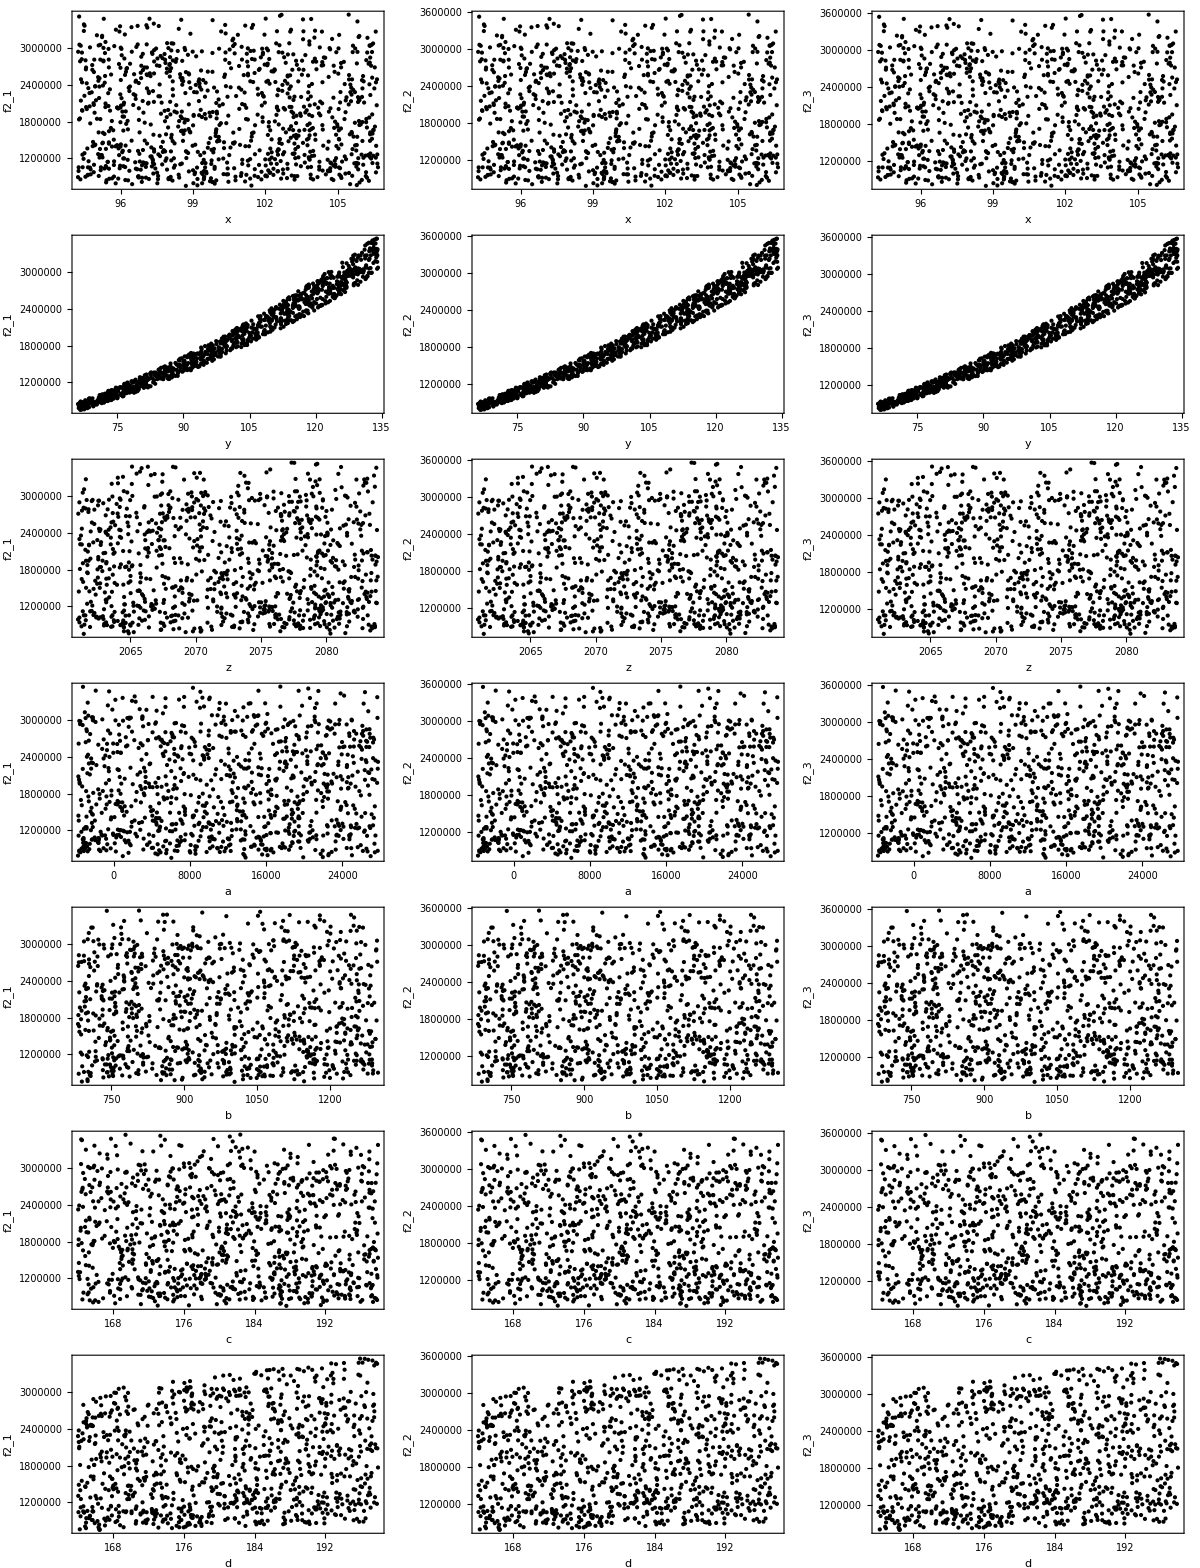

```mathematica
inhists
outhists
scatter//TableForm
```

## Sensitivity Analysis

#### Carry out matrix operations

We now set up the inputs and output tables, ready for the matrix operations

```mathematica
X=Table[Flatten[{Table[ins[[invar,i]],{invar,Nins}],1}],{i,Nruns}];
Do[Y[outvar,setting]=outs[[outvar,setting]],{outvar,Nouts},{setting,Nsets}];
(* The next command carries out the matrix operations to calculate the coefficients *)
(* This will give warnings if some of the inputs do not contribute significantly to the outputs, or if there is collinearity in the inputs (i.e. 2 or more inputs are approximately linearly correlated with each other) *)
(* Generally, these warnings are not fatal and are to be expected for more complicated datasets, however they can be avoided by removing the problematic inputs prior to running the notebook *)
Do[B[outvar,setting]=(Inverse[Transpose[X].X].Transpose[X]).Y[outvar,setting],{outvar,Nouts},{setting,Nsets}];
(* Now calculate the sensitivity indices for each input *)
Do[S[outvar,setting]=Table[B[outvar,setting][[invar]]*StandardDeviation[X[[;;,invar]]]/StandardDeviation[Y[outvar,setting]],{invar,Nins}],{outvar,Nouts},{setting,Nsets}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.00918×10^7, 1.00641×10^7, 2.0807×10^8, 1.17173×10^9, 9.86216×10^7, 1.81987×10^7, 1.81615×10^7, 100391.}, {1.00641×10^7, 1.046×10^7, 2.07804×10^8, 1.18248×10^9, 9.83786×10^7, 1.81684×10^7, 1.81411×10^7, 100265.}, « 5 », {100391., 100265., 2.07258×10^6, 1.16783×10^7, 982114., 181286., 180904., 1000.}} may contain significant numerical errors.

General::stop: Further output of Inverse :: luc will be suppressed during this calculation.

```mathematica
X[[1]]
```

{99.7674,85.7331,2077.24,11870.1,839.999,188.721,179.8,1}

```mathematica
B[1,1]
```

{11754.,1039.36,-7.56068,100.393,96.5639,123.797,-15.8924,-1.28526×10^6}

```mathematica
S[1,1]
```

{0.0464626,0.022589,-0.0000551785,0.997772,0.0186924,0.00129658,-0.00016795}

We will be reporting the sensitivity indices in two ways:

1) Sorted (top to bottom) by the value of S, for each setting, for each output variable
2) The same as the above, but sorted by |S|

Headers are required for the data tables

```mathematica
Do[Sheader[outvar,setting]={"Input","S("<>outlabels[[outvar,setting]]<>")"},{outvar,Nouts},{setting,Nsets}];
```

```mathematica
GSAheader="GSA - Sorted by S";
GSAabsheader="GSA - Sorted by abs(S)";
```

The following lines sort the sensitivity indices by either their true value, or their absolute value

```mathematica
Do[sorted[outvar,setting]=Prepend[Sort[Table[{inlabels[[invar]],S[outvar,setting][[invar]]},{invar,Nins}],#1[[2]]>#2[[2]]&],{Style[Sheader[outvar,setting][[1]],14,Bold,FontFamily->"Helvetica"],Style[Sheader[outvar,setting][[2]],14,Bold,FontFamily->"Helvetica"]}],{outvar,Nouts},{setting,Nsets}]
```

```mathematica
Do[abssorted[outvar,setting]=Prepend[Sort[Table[{inlabels[[invar]],S[outvar,setting][[invar]]},{invar,Nins}],Abs[#1[[2]]]>Abs[#2[[2]]]&],{Style[Sheader[outvar,setting][[1]],14,Bold,FontFamily->"Helvetica"],Style[Sheader[outvar,setting][[2]],14,Bold,FontFamily->"Helvetica"]}],{outvar,Nouts},{setting,Nsets}]
```

These sorted values are then combined to give tables of tables (one entry per output variable)

```mathematica
Do[Stab[outvar]=Table[Flatten[Table[sorted[outvar,setting][[i,;;]],{setting,Nsets}]],{i,Nins+1}],{outvar,Nouts}];
```

```mathematica
Do[Sabstab[outvar]=Table[Flatten[Table[abssorted[outvar,setting][[i,;;]],{setting,Nsets}]],{i,Nins+1}],{outvar,Nouts}]
```

The following commands define some eye-pleasing plots and tables

```mathematica
GSAS:=Module[{},Print[Style[GSAheader,16,Bold,FontFamily->"Helvetica"]];
Do[Print[Stab[outvar]//TableForm],{outvar,Nouts}]];
```

```mathematica
GSAabsS:=Module[{},Print[Style[GSAabsheader,16,Bold,FontFamily->"Helvetica"]];
Do[Print[Sabstab[outvar]//TableForm],{outvar,Nouts}]];
```

```mathematica
Export["GSA.xls",{GSAheader->Flatten[Join[Table[ReplacePart[Stab[outvar],1->Flatten[Table[Sheader[outvar,setting],{setting,Nsets}]]],{outvar,Nouts}]],1],GSAabsheader->Flatten[Join[Table[ReplacePart[Sabstab[outvar],1->Flatten[Table[Sheader[outvar,setting],{setting,Nsets}]]],{outvar,Nouts}]],1]},"XLS"]
```

GSA.xls

```mathematica
GSAColours={RGBColor[0,0,0],RGBColor[17.6/100,41.6/100,63.1/100],RGBColor[86.3/100,13.3/100,19.6/100],RGBColor[34.9/100,66.7/100,33.3/100],RGBColor[55.3/100,27.5/100,55.7/100],Orange,RGBColor[55.7/100,57.3/100,56.9/100],Brown};
```

```mathematica
Do[GSAsortedabs[outvar]=Sort[Table[{inlabels[[invar]],S[outvar,1][[invar]]},{invar,Nins}],Abs[#1[[2]]]<Abs[#2[[2]]]&],{outvar,Nouts}];
```

Note that if only one output setting is provided (e.g. the outputs don’t vary with time), then bar charts are produced for each output variable (sorted by |S| values - often referred to as a “Tornado Chart”, due to the shape). If there are multiple settings, list plots are provided instead, each containing data for each output setting value

```mathematica
GSAplot=If[Nsets==1,
{Table[BarChart[GSAsortedabs[outvar][[;;,2]],ChartStyle->Directive[Blue,Opacity[0.4]],BarOrigin->Left,Frame->True,Axes->False,FrameStyle->Directive[16,FontFamily->"Helvetica"],ChartLabels->None,FrameTicks->{Automatic,Table[{i,GSAsortedabs[outvar][[i,1]],0},{i,Nins}],Automatic,None},FrameLabel->{Style["s_i",Bold]},PlotLabel->Style[Labels[[outvar]],18,Bold,FontFamily->"Helvetica"],ImageSize->400],{outvar,Nouts}]}//TableForm
,
{Table[ListPlot[Table[Table[{setting,S[outvar,setting][[invar]]},{setting,Nsets}],{invar,Nins}],PlotRange->{{0,Last[SettingsVals]+First[SettingsVals]},All},Joined->True,PlotStyle->GSAColours,PlotMarkers->{{●,12}},PlotLegends->Placed[Table[Style[inlabels[[invar]],14,FontFamily->"Helvetica"],{invar,Nins}],Right],Frame->True,FrameStyle->Directive[16,FontFamily->"Helvetica"],FrameLabel->{Style[SettingsUnits,Bold],Rotate[Style["s_i",Bold],-90*Degree]},PlotLabel->Style[Labels[[outvar]],18,Bold,FontFamily->"Helvetica"],ImageSize->400],{outvar,Nouts}]}//TableForm];
Export["GSAplot.png",GSAplot];
```

#### Display SA Results

```mathematica
GSAS
GSAabsS
```

GSA - Sorted by S

Input | S(f1_1) | Input | S(f1_2) | Input | S(f1_3)
a | 0.997772 | a | 0.997983 | a | 0.997719
x | 0.0464626 | x | 0.0464744 | x | 0.0464641
y | 0.022589 | c | 0.0230116 | c | 0.0447145
b | 0.0186924 | y | 0.0225975 | y | 0.0225954
c | 0.00129658 | b | 0.0187013 | b | 0.0187013
z | -0.0000551785 | z | 0.00126882 | z | 0.00259215
d | -0.00016795 | d | -0.000166496 | d | -0.000164963

Input | S(f2_1) | Input | S(f2_2) | Input | S(f2_3)
y | 0.984092 | y | 0.98416 | y | 0.984226
d | 0.136001 | d | 0.136011 | d | 0.13602
c | 0.00427698 | c | 0.00559195 | c | 0.00690708
b | 0.00191967 | b | 0.00191763 | b | 0.00191559
z | 0.0000394292 | z | 0.000040782 | z | 0.0000421349
x | -0.00378829 | x | -0.002893 | x | -0.00199758
a | -0.00415419 | a | -0.00415303 | a | -0.00415186

GSA - Sorted by abs(S)

Input | S(f1_1) | Input | S(f1_2) | Input | S(f1_3)
a | 0.997772 | a | 0.997983 | a | 0.997719
x | 0.0464626 | x | 0.0464744 | x | 0.0464641
y | 0.022589 | c | 0.0230116 | c | 0.0447145
b | 0.0186924 | y | 0.0225975 | y | 0.0225954
c | 0.00129658 | b | 0.0187013 | b | 0.0187013
d | -0.00016795 | z | 0.00126882 | z | 0.00259215
z | -0.0000551785 | d | -0.000166496 | d | -0.000164963

Input | S(f2_1) | Input | S(f2_2) | Input | S(f2_3)
y | 0.984092 | y | 0.98416 | y | 0.984226
d | 0.136001 | d | 0.136011 | d | 0.13602
c | 0.00427698 | c | 0.00559195 | c | 0.00690708
a | -0.00415419 | a | -0.00415303 | a | -0.00415186
x | -0.00378829 | x | -0.002893 | x | -0.00199758
b | 0.00191967 | b | 0.00191763 | b | 0.00191559
z | 0.0000394292 | z | 0.000040782 | z | 0.0000421349

NOTE: if there are multiple settings within a particular output (e.g. if we have a model “f1” which produces outputs at t=1,2,3), then a line plot will be shown with sensitivities at each setting. If there is only one setting (e.g. t=1 only), then a bar chart will be produced instead. A plot will be produced for each model (f1, f2, f3...)

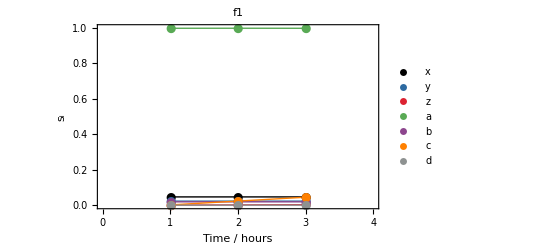
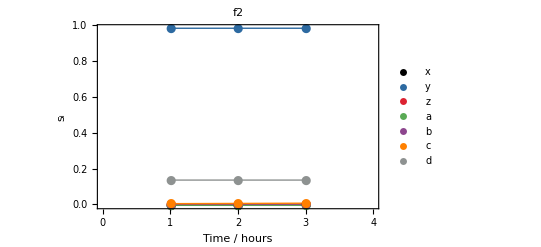
-Graphics- | -Graphics-

```mathematica
GSAplot
```